```mathematica
G[u_,v_,J_,K_]:= (2 u K)/(v-u +v J +u K+√((v-u+v J+u K)^2-4(v-u)u  K))(*Goldbeter-KoshLand*)
```

```mathematica
sys1:= D[R[t],t]== k0  G[k3 ,k4 R[t],J3,J4] - k2  R[t] S (*ode*)
```

```mathematica
parameter:= {k0-> 1,k2-> 1 ,k3-> 0.5, k4->1 , J3-> 0.01, J4-> 0.01}(*parameters*)
```

```mathematica
b1=Solve[sys1[[2]]==0/.parameter,R[t]];(*solution for the nullclines*)
```

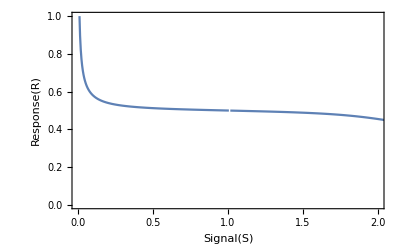

```mathematica
p1=Plot[Evaluate[{R[t]/.b1[[1]]}],{S,0,15},PlotRange->{{0,2},{0,1}},PlotRangeClipping->True,Frame->True,FrameLabel->{"Signal(S)","Response(R)"},LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
List@@sys1[[2]](*pdes as a list *)
```

{-k2 S R[t],(2 J4 k0 k3)/(-k3+J4 k3+k4 R[t]+J3 k4 R[t]+√(-4 J4 k3 (-k3+k4 R[t])+(-k3+J4 k3+k4 R[t]+J3 k4 R[t])^2))}

```mathematica
tmp1 = Cases[List@@sys1[[2]],n1_ /; If[Length[n1]>1,n1[[1]]==-1]](*negative part*)
```

{-k2 S R[t]}

```mathematica
deg2 = - Plus@@tmp1
```

k2 S R[t]

```mathematica
prod2 = Plus@@Complement[List@@sys1[[2]],tmp1](*positive part*)
```

(2 J4 k0 k3)/(-k3+J4 k3+k4 R[t]+J3 k4 R[t]+√(-4 J4 k3 (-k3+k4 R[t])+(-k3+J4 k3+k4 R[t]+J3 k4 R[t])^2))

```mathematica
Plot[{(deg2 /. parameter) /. S->0.5,(deg2 /. parameter) /. S->1,(deg2 /. parameter) /. S->1.5, prod2 /. parameter},{R[t],0,1},Frame->True,PlotRange->{{0,1},{0,1.2}},PlotRangeClipping->True, PlotStyle->{{Black},{Black},{Black},{Dashed,Black}},FrameLabel->{"R","Rate(dR/dt)"},LabelStyle->{GrayLevel[0],Bold}](*Rate Curve*)
```